```mathematica
int = {-0.340483, -0.095788, -0.036596, -0.018925, -0.011026, -0.006550, -0.003856, -0.002251, -0.001277, -0.000728, -0.000413, -0.000233, -0.000132};
err = {0.000125, 0.000089, 0.000058, 0.000037, 0.000022, 0.000013, 0.000007, 0.000014, 0.000010, 0.000006, 0.000003, 0.000003, 0.000002};

i[n_] := Part[int,n];
e[n_] := Part[err,n];
s[n_] := Sum[i[m], {m,1,n}]
es[n_] := Sqrt[Sum[Part[err,m]^2, {m,1,n}]]
r[n_] := i[n]/i[n-1]
naive[n_] := s[n-1]+i[n]/(1-r[n])
nerr[n_] := Sqrt[es[n-2]^2+(i[n-1](i[n-1]-2i[n])e[n-1]/(i[n-1]-i[n])^2)^2 +(i[n-1]^2 e[n]^2/(i[n-1]-i[n])^2)^2]

table = Table[{i[n],e[n],s[n], es[n], If[n>1, naive[n],0], If[n>1, nerr[n],0]},{n,1,13}]//MatrixForm
```

(-0.340483 | 0.000125 | -0.340483 | 0.000125 | 0 | 0
-0.095788 | 0.000089 | -0.436271 | 0.000153447 | -0.473768 | 0.000105845
-0.036596 | 0.000058 | -0.472867 | 0.000164043 | -0.495493 | 0.000136557
-0.018925 | 0.000037 | -0.491792 | 0.000168164 | -0.51206 | 0.000153684
-0.011026 | 0.000022 | -0.502818 | 0.000169597 | -0.518209 | 0.000167754
-0.00655 | 0.000013 | -0.509368 | 0.000170094 | -0.518953 | 0.000170028
-0.003856 | 7.×10^-6 | -0.513224 | 0.000170238 | -0.518743 | 0.000170144
-0.002251 | 0.000014 | -0.515475 | 0.000170813 | -0.518632 | 0.000170229
-0.001277 | 0.00001 | -0.516752 | 0.000171105 | -0.518426 | 0.000170535
-0.000728 | 6.×10^-6 | -0.51748 | 0.00017121 | -0.518445 | 0.000170981
-0.000413 | 3.×10^-6 | -0.517893 | 0.000171237 | -0.518434 | 0.00017116
-0.000233 | 3.×10^-6 | -0.518126 | 0.000171263 | -0.518428 | 0.000171222
-0.000132 | 2.×10^-6 | -0.518258 | 0.000171275 | -0.518431 | 0.00017125)

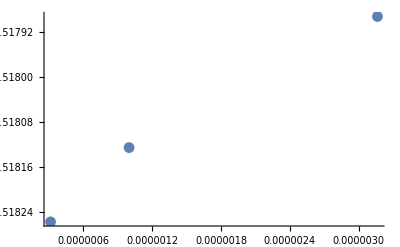

```mathematica
ListPlot[Table[{Sqrt[1/10]^n,s[n]},{n,11,13}], PlotRange -> {-0.51788, -0.51846}]
```

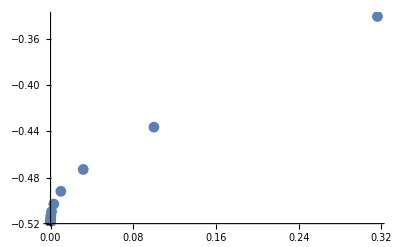

```mathematica
ListPlot[Table[{Sqrt[1/10]^n,s[n]},{n,1,13}], PlotRange -> {-.47, -.52}]
```

```mathematica
data1 = Table[{Sqrt[1/10]^n,s[n]},{n,1,13}];
data2 = Table[{Sqrt[1/10]^n,s[n]},{n,6,13}];
data3 = Table[{Sqrt[1/10]^n,s[n]},{n,8,13}];
```

```mathematica
sqt = Fit[data1, {1, Sqrt[n]},n]
```

-0.51999+0.302975 √n

```mathematica
line = Fit[data1, {1, n},n]
```

-0.510032+0.561343 n

```mathematica
parabola =  Fit[data1, {1, n, n^2},n]
```

-0.513028+0.966956 n-1.33768 n^2

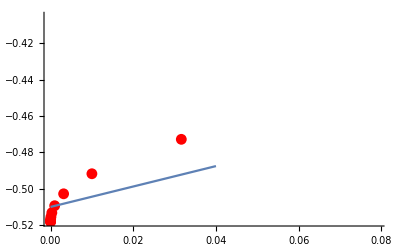

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[line,{n,0,0.04}]]
```

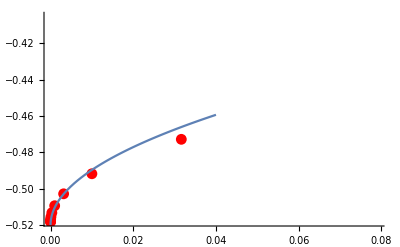

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[sqt,{n,0,0.04}]]
```

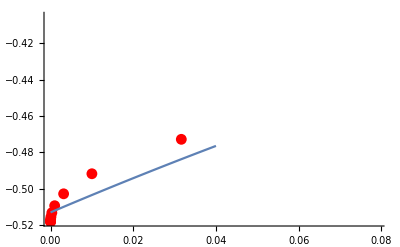

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[parabola,{n,0,0.04}]]
```

```mathematica
cubic =  Fit[data1, {1, n, n^2, n^3},n]
```

-0.515042+1.86509 n-13.8969 n^2+30.8154 n^3

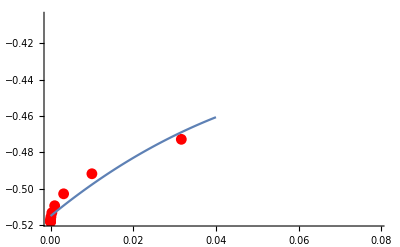

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[cubic,{n,0,0.04}]]
```

-0.517052+6.42182 n-540.817 n^2+16432.7 n^3-147824. n^4+319650. n^5

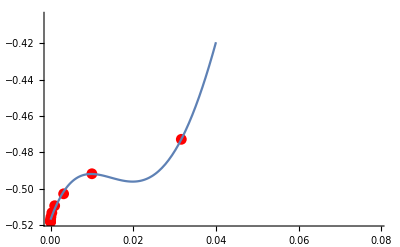

```mathematica
funf=  Fit[data1, {1, n, n^2, n^3, n^4, n^5},n]
Show[ListPlot[data1,PlotStyle->Red],Plot[funf,{n,0,0.04}]]
(*Regress[data1, {1, n, n^2, n^3, n^4, n^5},n,RegressionReport]*)
```

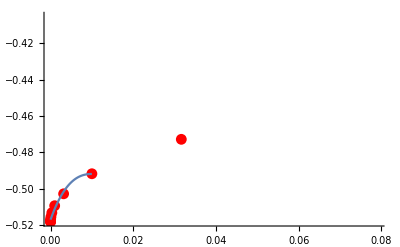

-0.518429+0.304814 √n-1.7447 n+121.587 n^(3/2)-4891.32 n^2+94408.5 n^(5/2)-889756. n^3+3.93476×10^6 n^(7/2)-6.73092×10^6 n^4+6.52497×10^6 n^5

-Graphics-

```mathematica
Show[ListPlot[data1,PlotStyle->Red],Plot[funf,{n,0,0.01}]]






cmplx =Fit[data1, {1,n^(1/2), n,n^(3/2), n^2,n^(5/2), n^3,n^(6/2), n^4,n^(7/2), n^5},n]
Show[ListPlot[data1,PlotStyle->Red],Plot[funf,{n,0,0.04}]]
```

-0.519362+0.0946404 n^(1/3)

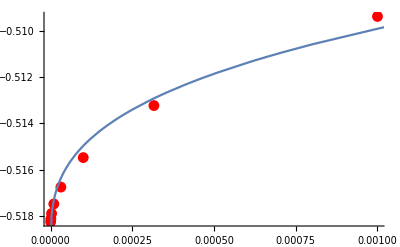

```mathematica
rt3=  Fit[data2, {1,n^(1/3) },n]
Show[ListPlot[data2,PlotStyle->Red],Plot[rt3,{n,0,0.01}]]
```

-0.518386+0.28677 √n

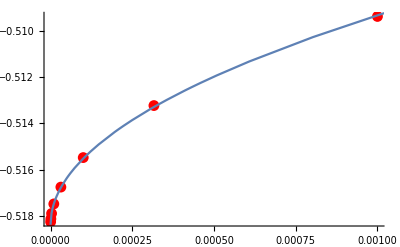

```mathematica
rt2=  Fit[data2, {1,n^(1/2) },n]
Show[ListPlot[data2,PlotStyle->Red],Plot[rt2,{n,0,0.01}]]
```

-0.505109+0.000979458 Log[n]

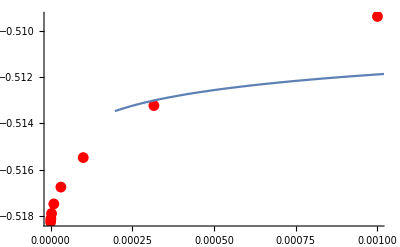

```mathematica
lg2=  Fit[data2, {1,Log[8,n] },n]
Show[ListPlot[data2,PlotStyle->Red],Plot[lg2,{n,0,0.01}]]
```

-0.518418+0.294884 √n

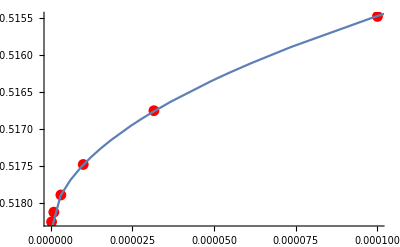

```mathematica
rtt2=  Fit[data3, {1,n^(1/2) },n]
Show[ListPlot[data3,PlotStyle->Red],Plot[rtt2,{n,0,0.01}]]
```

```mathematica
par3=  Fit[data3, {1,n^(1/2) },n]
Show[ListPlot[data3,PlotStyle->Red],Plot[par3,{n,0,0.01}]]
```

-0.518418+0.294884 √n

-Graphics-